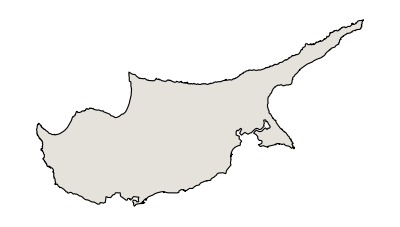
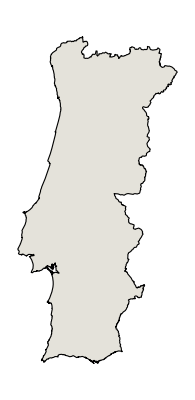
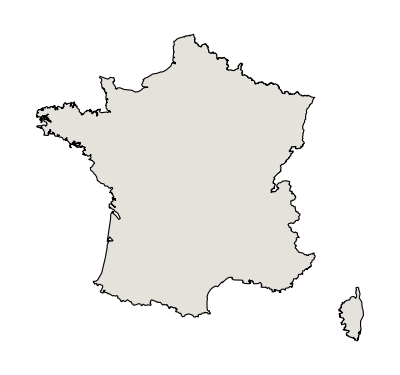
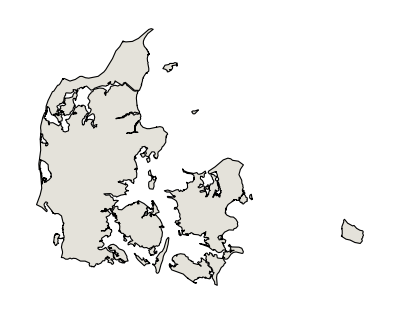
{{Cyprus,124.679 people/km^2,-Graphics-},{Portugal,116.248 people/km^2,-Graphics-},{France,116.231 people/km^2,-Graphics-},{Denmark,130.62 people/km^2,-Graphics-}}

```mathematica
Map[{#[[1]],CountryData[#[[1]],"Population"]/CountryData[#[[1]],"Area"],CountryData[#[[1]],"Shape"]}&,SortBy[{#,Abs[CountryData["Poland","Population"]/CountryData["Poland","Area"]-CountryData[#,"Population"]/CountryData[#,"Area"]]}&/@CountryData["EU"],Last][[2;;5]]]
```

```mathematica
ArrayPlot[CellularAutomaton[{10,2 ,{1,1}},{{1}, 0},101]]
```

-Graphics-

```mathematica
ArrayPlot[board=Last[CellularAutomaton[{10,2,{1,1}}, RandomInteger[1,{100,100}], {102}]]]
```

-Graphics-

```mathematica
RulePlot[CellularAutomaton[{10,2,{1,1}}, RandomInteger[1,{100,100}], {102}]]
```

```mathematica
liczba=200000;
rand=RandomInteger[15^20];
array={liczba,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
board=RandomInteger[1,{400,400}] RandomInteger[1,{400,400}];
Dynamic[ArrayPlot[board=Last[CellularAutomaton[array,board,{{0,1}}]]]]
```